# Conformal Data From Direct Diagonalization

```mathematica
Do[σ[a]=SparseArray@PauliMatrix[a],{a,0,3}];
CircleTimes=KroneckerProduct;
𝕀[a_]:=IdentityMatrix[2^a,SparseArray];
```

Permutation operator (useful to build a translation operator by multiplying several of these):

```mathematica
P[L_][a_]:=∑_(n=0)^3 1/2 𝕀[a-1]⊗σ[n]⊗σ[n]⊗𝕀[L-1-a];
```

Creating H and shift operator for L=6 up to 12:

```mathematica
Monitor[Do[
ℍ[L]=-(1/L∑_(n=0)^(L-2) 𝕀[n]⊗σ[1]⊗σ[1]⊗𝕀[L-2-n]+1/L σ[1]⊗𝕀[L-2]⊗σ[1]+1/L∑_(n=0)^(L-1) 𝕀[n]⊗σ[3]⊗𝕀[L-1-n])//N;
𝕋[L]=Dot@@Table[P[L][a],{a,L-1}];
,{L,4,12}],L]//Timing
```

{0.880037,Null}

Here we shift H (such that all energies are positive) and multiply by ⅇ^(ⅈ P) such that the eigenvalues’ abs and arg will yield the energies and the momenta. This tricks lifts the degeneracies.

```mathematica
ClearAll[ev]
ev[L_]:=ev[L]=(ℍ[L]+10𝕀[L]).𝕋[L]//Eigensystem//Transpose//SortBy[#,Abs]&//Take[#,12]&//Transpose;
```

From here on we focus on some fixed length L. For L=12 it takes about a minutes.

```mathematica
𝕃=10;
```

```mathematica
energies=ev[𝕃]⟦1⟧//Abs
```

{8.72151,8.73725,8.84666,8.86086,8.86086,8.96568,8.96568,8.96568,8.96568,8.97236,8.97236,8.98446}

According to Wilke’s prescription for the relation between momenta and spin:

```mathematica
spins=ev[𝕃]⟦1⟧//Arg[#] 𝕃/(2π)&//Rationalize[#,10^-3]&
```

{0,0,0,-1,1,-1,1,-2,2,-2,2,0}

```mathematica
spins=ev[𝕃]⟦1⟧//Arg[#] 𝕃/(2π)&//Mod[#,𝕃/2,-𝕃/4]&//Rationalize[#,10^-3]&
```

{0,0,0,-1,1,-1,1,-2,2,-2,2,0}

```mathematica
both={spins,energies}ᵀ//Sort[#,#1⟦2⟧<#2⟦2⟧&]&
```

{{0,8.72151},{0,8.73725},{0,8.84666},{1,8.86086},{-1,8.86086},{2,8.96568},{-2,8.96568},{1,8.96568},{-1,8.96568},{2,8.97236},{-2,8.97236},{0,8.98446}}

Assume that the lowest spin 2 is the stress tensor. Then it is position n in the list where n is:

```mathematica
theT=both//Position[#,{2,a_}]&//#⟦1,1⟧&
```

6

the properly normalized spectra is then

```mathematica
finally=both/.{a_,b_}:>{a,2(b-both⟦1,2⟧)/(both⟦theT,2⟧-both⟦1,2⟧)}
```

{{0,0.},{0,0.128929},{0,1.02509},{1,1.14139},{-1,1.14139},{2,2.},{-2,2.},{1,2.},{-1,2.},{2,2.05475},{-2,2.05475},{0,2.15386}}

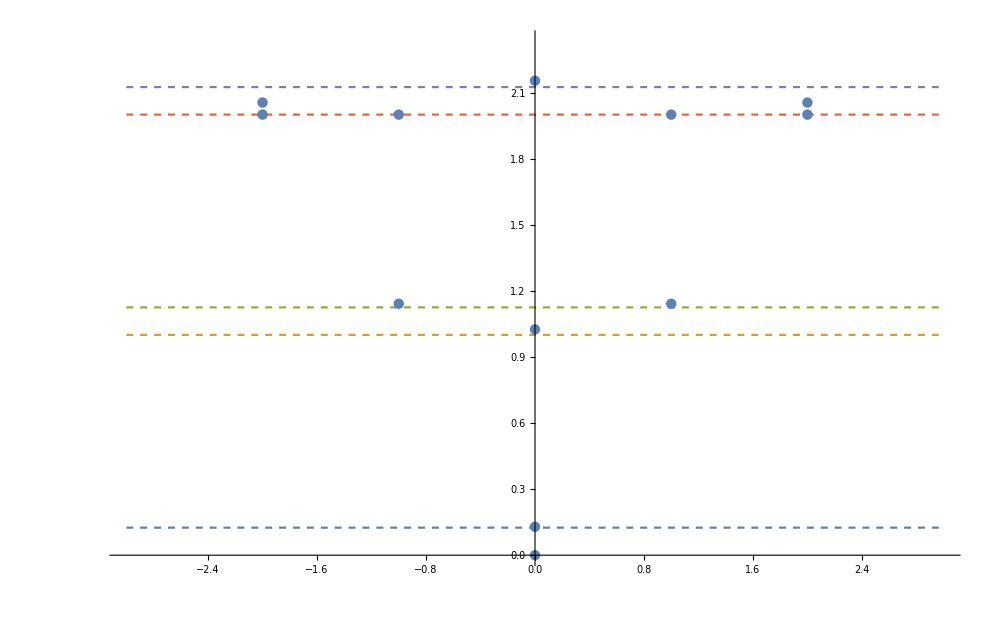

```mathematica
Show[Plot[{1/8,1,1+1/8,2,2+1/8},{x,-3,3},PlotStyle->Dashed],finally//ListPlot[#,PlotRange->All,PlotStyle->{PointSize[0.0075]}]&,PlotRange->{{-3,3},{0,2+1/3}},ImageSize->1000]
```

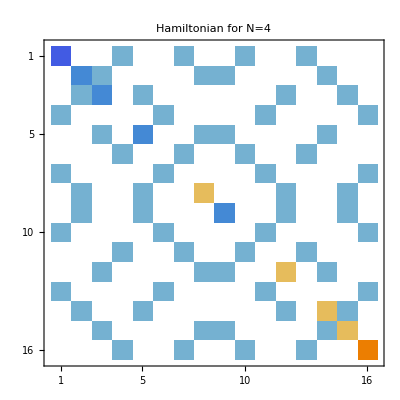
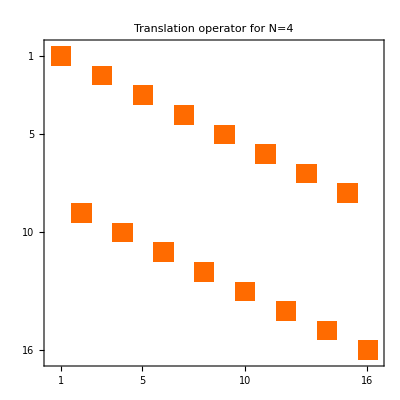

```mathematica
plots={ℍ[4]//MatrixPlot[#,PlotLabel->"Hamiltonian for N=4"]&,𝕋[4]//MatrixPlot[#,PlotLabel->"Translation operator for N=4"]&}
```